# Plotting Allele Surfing 2_28_17

This program plots particular data outputs from the simulations allele surfing 2_28_17.

## Plotting Population Sizes

```mathematica
nPop=1;
```

```mathematica
stData=Import["/Users/ailenemacpherson/Documents/workspace/AlleleSurfing3_13/data5.csv"][[;;,1;;nPop]];
```

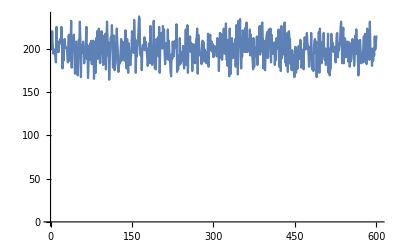

```mathematica
ListLinePlot[Transpose[stData],AxesOrigin->{0,0}]
```

```mathematica
GeometricMean[Transpose[stData]//Flatten]//N
```

198.229

```mathematica
Length[stData]
```

602

## Plotting Coalescent

### Distributions of Coalescent times in a Single population

```mathematica
nPop=1;
gmax=600;
nIndList=Flatten[Transpose[Import["/Users/ailenemacpherson/Documents/workspace/AlleleSurfing3_13/data0.csv"][[;;,1;;nPop]]]];
nInd0=nIndList[[1]];
nIndF=nIndList[[gmax+1]];
(*Important coalescent data.Each column represents the history of the different lineage.This generation in this history is captured by three rows:row 3*g+1:lineage population in generation g.row 3*g+2:lineage individual in generation g,row 3*g+2:lineage chromosome in generation g.*)
cData=Import["/Users/ailenemacpherson/Documents/workspace/AlleleSurfing3_13/coal0.csv"][[1;;3(gmax+2),1;;2*nIndF]];
sampleSize=3;
testSample=RandomSample[Range[2*nIndF],sampleSize]
```

{373,135,221}

plotData combines the info from the three identity pieces of information (population, individual, chromosome).  Each row is an lineage, each column is a generation, sub column 1= locus identity, sub column 2 is the generation.

```mathematica
plotData=Transpose[Table[{cData[[3*g+3,i]]+2*cData[[3*g+2,i]]+(2*nInd0)cData[[3*g+1,i]],gmax+1-g},{g,0,gmax+1},{i,1,2*nIndF}]];
```

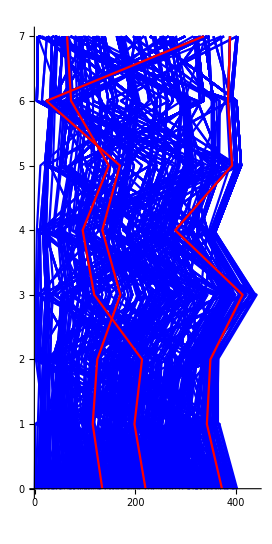

```mathematica
AllLineages=ListLinePlot[plotData[[;;,595;;-1]],PlotStyle->Blue,AxesOrigin->{-1,0},AspectRatio->2];
SelectedLineages=ListLinePlot[plotData[[testSample]][[;;,595;;-1]],PlotStyle->{Red},AxesOrigin->{-1,0},AspectRatio->2];
Show[AllLineages,SelectedLineages]
```

```mathematica
Tlist[testSample]
```

{{3,31},{2,571}}

### Calculating coalescent times for a sub-sample of the data:

For the sub-sample each row is a generation each column is an individual and the sub columns give locus identity and generation

```mathematica
Tlist[sample_]:=Block[{s,g,Tlist,T,nDistinct,sampleData},Tlist={};
sampleData=Transpose[plotData[[sample]]][[;;,;;,1]];
nDistinct=Table[CountDistinct[sampleData[[r]]],{r,1,gmax+2}];
g=gmax+2;
For[s=nDistinct[[gmax+2]],s>=nDistinct[[1]],s--,T=0;
While[nDistinct[[g]]==s,
g--;T++;
];
AppendTo[Tlist,{s,T}];
];
Tlist
];
```

```mathematica
Tlist[testSample]
```

{{3,115},{2,20},{1,467}}

#### Distribution of coalescent times:

Given a particular demographic history as described by nInd we can calculate the probability distribution of coalescent times by resampling.

```mathematica
TLIST[nRep_]:=Module[{rep,TLIST},TLIST={};
For[rep=1,rep≤nRep,rep++,
sample=RandomSample[Range[nIndF*2],sampleSize];
AppendTo[TLIST,Tlist[sample]];.10
]; TLIST
];
```

```mathematica
TLIST[2]
```

{{{3,115},{2,148},{1,339}},{{3,115},{2,20},{1,467}}}

```mathematica
distData=TLIST[2000][[;;,1;;2,2]];
```

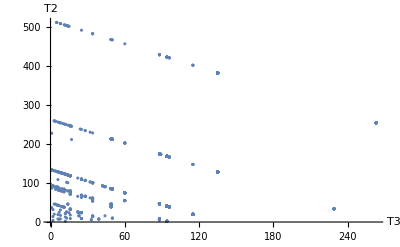

```mathematica
ListPlot[Select[distData,Total[#]<600&],AxesLabel->{"T3","T2"}]
```

```mathematica
Histogram3D[Select[distData,Total[#]<600&],PlotTheme->"Scientific",AxesLabel->{"T3","T2","Prob"}]
```

-Graphics3D-

### Distribution from multiple simulations

```mathematica
Tlist2[sampleData_]:=Block[{s,g,Tlist,T},Tlist={};
nDistinct=Table[CountDistinct[sampleData[[r]]],{r,1,gmax+2}];
g=gmax+2;
For[s=nDistinct[[gmax+2]],s>=nDistinct[[1]],s--,T=0;
While[nDistinct[[g]]==s,
g--;T++;
];
AppendTo[Tlist,{s,T}];
];
Tlist
];
```

```mathematica
nPop=1;
gmax=600;
nRep=500;
sampleSize=3;
Module[{r,tList},TLIST={};
For[r=0,r<nRep,r++,
nIndList=Flatten[Transpose[Import[StringJoin["/Users/ailenemacpherson/Documents/workspace/AlleleSurfing3_13/data",ToString[r],".csv"]][[;;,1;;nPop]]]];
nInd0=nIndList[[1]];
nIndF=nIndList[[gmax+1]];
cData=Import[StringJoin["/Users/ailenemacpherson/Documents/workspace/AlleleSurfing3_13/coal",ToString[r],".csv"]][[1;;3(gmax+2),1;;2*nIndF]];
sample=RandomSample[Range[2nIndF],sampleSize];
sampleData=Table[cData[[3*g+3,i]]+2*cData[[3*g+2,i]]+(2*nInd0)cData[[3*g+1,i]],{g,0,gmax+1},{i,1,2*nIndF}][[;;,sample]];
tList=Tlist2[sampleData];If[nDistinct[[1]]==1,AppendTo[TLIST,tList]];
]
]
```

```mathematica
TLIST;
```

```mathematica
TlistSave;
```

```mathematica
distData=Select[TLIST[[;;,{2,1},2]],#[[1]]+#[[2]]<600&];
```

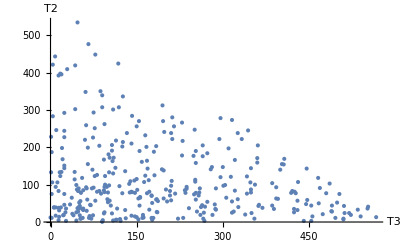

```mathematica
ListPlot[distData,AxesLabel->{"T3","T2"}]
```

```mathematica
Histogram3D[distData,AxesLabel->{"T2","T3","Prob"}]
```

-Graphics3D-

### Griffiths and Tavere predicted distribution

```mathematica
m[t_]:=2*200;
v[τ_]:=m[Floor[m[0]τ]]/m[0]
(*Note the change of Λ to a sum rather than an integral*)
Λ[x_]:=Integrate[1/v[τ],{τ,0,x}];
s[j_,i_,τVec_]:=If[j<i,Sum[τVec[[k]],{k,j,i}],If[j==i,τVec[[i]],0]];
g[i_,τVec_]:=N[Product[Binomial[j,2]/v[s[j,i,τVec]] Exp[-Binomial[j,2](Λ[s[j,i,τVec]]-Λ[s[j+1,i,τVec]])],{j,2,i}]]
```

```mathematica
f[i_,τVec_]:=N[Product[Binomial[j,2]Exp[-Binomial[j,2]τVec[[j]]],{j,2,i}]]
```

```mathematica
distSpace[max_]:=RandomReal[max,{10000,2}]
```

```mathematica
DSpace=Select[distSpace[1.5],#1⟦1⟧+#1⟦2⟧≤1.5&];
```

```mathematica
Histogram3D[DSpace]
```

-Graphics3D-

```mathematica
predDist=Table[Join[DSpace[[i]],{g[3,Join[{0},DSpace[[i]]]]}],{i,1,Length[DSpace]}];
```

```mathematica
predDist2=Table[Join[DSpace[[i]],{f[3,Join[{0},DSpace[[i]]]]}],{i,1,Length[DSpace]}];
```

```mathematica
ListPlot3D[predDist2,Mesh->None,AxesLabel->{"T2","T3","Prob"},InterpolationOrder->1]
```

-Graphics3D-

Note that axes scaling is in terms of the number of individuals per generation.  Hence T3=1.5 means 1.5*m[0].

### Hypothesis testing

Constant population size likelihood

```mathematica
Hconst[popSize_]:=Block[{i,m,v,Λ,s,g,L},L=0;
m[t_]:=2*popSize;
v[τ_]:=m[Floor[m[0]τ]]/m[0];
Λ[x_]:=Integrate[1/v[τ],{τ,0,x}];
s[j_,i_,τVec_]:=If[j<i,Sum[τVec[[k]],{k,j,i}],If[j==i,τVec[[i]],0]];
g[i_,τVec_]:=N[Product[Binomial[j,2]/v[s[j,i,τVec]] Exp[-Binomial[j,2](Λ[s[j,i,τVec]]-Λ[s[j+1,i,τVec]])],{j,2,i}]];
For[i=1,i≤Length[distData],i++,
L+=g[3,1/m[0] Join[{0},distData[[i]]]];
];
L
]
```

```mathematica
Hconst[200]
```

368.675